```mathematica
f[x_]:=x^2 Cos[x];
window={{1.2,1.8},{-1,1}};
secantleft=window[[1,1]];
secantright=window[[1,2]];
secantgraphs={f[secantleft]+(f[secantleft]-f[secantright])/(secantleft-secantright)(x-secantleft)};
secantpoints={};
secantcount=0;
newtonguess=1.3;
newtongraphs={};
newtonpoints={};
newtoncount=0;
```

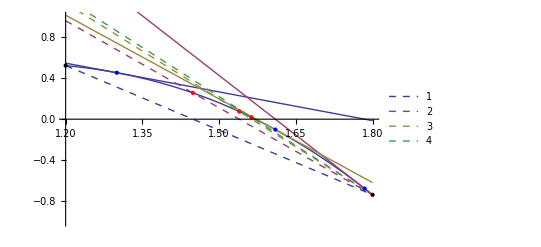

0.00750409 Secant absolute error after 3 iterations 
0.00179914 Newton absolute error after 3 iterations

```mathematica
secantcount++;
secantguess=secantleft-f[secantleft](secantleft-secantright)/(f[secantleft]-f[secantright]);
(*logic:*)
(*To use swapping uncomment the below conditional*)
(*If[Abs[f[secantleft]]>Abs[f[secantright]],secantleft=secantguess,secantright=secantguess];*)
(*To use false position method uncomment the below conditional*)
(*If[f[secantguess]*f[secantleft]>0,secantleft=secantguess,secantright=secantguess];*)
(*To use naive secant method uncomment the below*)
(*secantleft=secantright;secantright=secantguess;*)
(***)

secantpoints=Append[secantpoints,{secantguess,f[secantguess]}];
secantgraphs=Append[secantgraphs,f[secantleft]+(f[secantleft]-f[secantright])/(secantleft-secantright)(x-secantleft)];

newtoncount++;
newtonpoints=Append[newtonpoints,{newtonguess,f[newtonguess]}];
newtongraphs=Append[newtongraphs,f[newtonguess]+f'[newtonguess](x-newtonguess)];
newtonguess=newtonguess-f[newtonguess]/f'[newtonguess];

Show[Plot[f[x],{x,window[[1,1]],window[[1,2]]},PlotRange->window[[2]],ImageSize->Full],Plot[newtongraphs,{x,window[[1,1]],window[[1,2]]},PlotLegends->Placed[Automatic,Above]],Plot[secantgraphs,{x,window[[1,1]],window[[1,2]]},PlotLegends->Placed[Automatic,Below],PlotStyle->Dashed],ListPlot[secantpoints,PlotStyle->{Red,PointSize[Large]}],ListPlot[newtonpoints,PlotStyle->{Blue,PointSize[Large]}],ListPlot[{{window[[1,1]],f[window[[1,1]]]},{window[[1,2]],f[window[[1,2]]]}},PlotStyle->{Black,PointSize[Large]}]]
StringForm["`1` Secant absolute error after `3` iterations \n`2` Newton absolute error after `4` iterations",N[Abs[secantguess-π/2]],Abs[newtonguess-π/2],secantcount,newtoncount]
```